```mathematica
#Solving  u'(t) = -2*u(t) + 1; u(0)=1;
```

```mathematica
n=100;
```

```mathematica
Ys = Table[0,{n+1}];
Ys[[1]] = 1;
```

```mathematica
h=5./n;
```

```mathematica
Xs = Table [i*h, {i,0,n}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.}

```mathematica
For[i=2,i≤n+1,i++, Ys[[i]] = Ys[[i-1]] + h*(-2*Ys[[i-1]] + 1)]
```

```mathematica
Ys
```

{1,0.95,0.905,0.8645,0.82805,0.795245,0.765721,0.739148,0.715234,0.69371,0.674339,0.656905,0.641215,0.627093,0.614384,0.602946,0.592651,0.583386,0.575047,0.567543,0.560788,0.554709,0.549239,0.544315,0.539883,0.535895,0.532305,0.529075,0.526167,0.523551,0.521196,0.519076,0.517168,0.515452,0.513906,0.512516,0.511264,0.510138,0.509124,0.508212,0.50739,0.506651,0.505986,0.505388,0.504849,0.504364,0.503928,0.503535,0.503181,0.502863,0.502577,0.502319,0.502087,0.501879,0.501691,0.501522,0.501369,0.501233,0.501109,0.500998,0.500899,0.500809,0.500728,0.500655,0.50059,0.500531,0.500478,0.50043,0.500387,0.500348,0.500313,0.500282,0.500254,0.500228,0.500206,0.500185,0.500166,0.50015,0.500135,0.500121,0.500109,0.500098,0.500088,0.50008,0.500072,0.500065,0.500058,0.500052,0.500047,0.500042,0.500038,0.500034,0.500031,0.500028,0.500025,0.500022,0.50002,0.500018,0.500016,0.500015,0.500013}

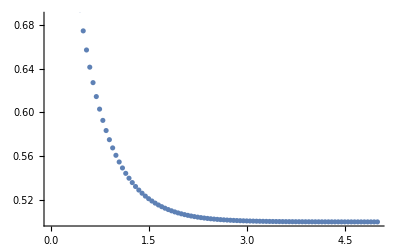

```mathematica
p1 = ListPlot[Transpose[{Xs,Ys}]-> all]
```

```mathematica
S[x_] =1/2* Exp[-2.*x]+1/2;
```

```mathematica
S[0.5]
```

0.68394

```mathematica
p2 = Plot[S[x],{x,0,5}];
```

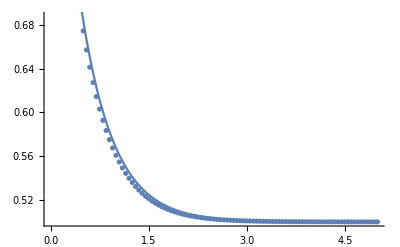

```mathematica
Show[p1,p2]
```